```mathematica
Delta[j_,k_]:=Sign[j]*KroneckerDelta[j,k];
Unprotect[Times];i[{x_}]*i[alpha_List]:=Sum[i[Insert[alpha,x,k]],{k,1,Length[alpha]+1}]+Sum[Delta[x,alpha[[k]]]*i[ReplacePart[alpha,0,k]],{k,1,Length[alpha]}];x_*(y_+z_):=x*y+x*z;
Unprotect[Power];
i[x_List]^n_Integer := Fold[Times, i[x], Table [i [x], {k, n - 1}]] /;n > 0;(x_ + y_)^n_Integer := Fold [Times, x + y, Table [x + y, {k, n - 1}]] /; n > 0; 
Protect [Power];
Ap[i[lista_List], n_Integer] := i[Append[lista, n]];
Ap[x_ +y_,n_] := Ap[x, n] + Ap[y, n];
Ap[m_*x_,n_] := m Ap[x, n]; 
i[alpha_List]*i[beta_List]:=Ap[i[alpha]*i [Drop [beta, -1]] , Last[beta]]+Ap[i[Drop[alpha, -1]]*i[beta], Last[alpha]] +Delta[Last[alpha], Last[beta]]*Ap[i[Drop[alpha, -1] ] *i[Drop[beta, -1]], 0] /;(Length[alpha] > 1 && Length [beta] > 1)

Protect[Times];
$RecursionLimit=Infinity;
Esp[i[x_List]]:=If[Total[x]==0,h^Length[x]/(Length[x])!,0]
Esp[a_+b_]:=Esp[a]+Esp[b]
Esp[n_*i[x_List]]:=n *Esp[i[x]]
j[{}]:=i[{}];
j[{x_}]:=i[{x}]
j[lista_List]:=Ap[j[Drop[lista,-1]],Last[lista]]+(1/2)Delta[Last[lista],Last[Drop[lista,-1]]] Ap[j[Drop[lista,-2]],0];
```

```mathematica
EspCond[a_+b_,c_]:=EspCond[a,c]+EspCond[b,c];
EspCond[(n_Integer|n_Rational)*a_,b_]:=n*EspCond[a,b];
ParseListiSave[x_List]:=ParseListiSave[x]=Module[{h={},l={}},Which[MatchQ[#,z[_]],AppendTo[h,#];AppendTo[l,0],MatchQ[#,_Integer],AppendTo[l,#],MatchQ[#,-i[_]],AppendTo[h,#];AppendTo[l,0]]&/@x;(Times@@h)*i[l]];
(*ParseListiSave[x_List]:=ParseListiSave[x]=Times@@(ReplaceAll[x,_Integer->1])*i[ReplaceAll[x,{z[_]->0,-i[_]->0}]];*)
ParseListi[x_List]:=ParseListiSave[Sort[x]];
EspCondSave[i[x_List],zl_]:=EspCondSave[i[x],zl]=Total[Esp[ParseListi[#]]&/@Flatten[Outer[List,##]&@@(If[#==0,{0},{#,-i[{1}],z[#]}]&/@x),Length[x]-1]]/.{h->1,z[0]->1,Sequence@@(MapThread[z[#1]->#2&,{Range[Length[zl]],zl}]//Flatten)};
EspCond[i[x_List],zl_]:=EspCondSave[i[Sort[x]],zl]; 
EspCond[jml[x_List],zl_]:=EspCond[Times@@(j/@x),zl];
```

```mathematica
EspCond[jml[{{1,1,1}}],{z}]
EspCond[jml[{{1,1,1}}],{5}]
```

z^3/6

125/6

```mathematica
Clear[x];
Diu[h_,y_]:=D[h,y]-h*y;
Diu[u_List,f_,x_]:=Nest[Diu[#,x]&,f,Length[u]];
DA[phi_,m_,x_]:=Which[m==0,bx*D[phi,x],m==1,sigx*D[phi,x]];
CA[index_,gx_,x_,x0_]:=Fold[DA[#1,#2,x]&,If[index[[1]]==0,bx,gx],Rest[index]]/.x->x0;
Sk[k_]:=Module[{jl=IntegerPartitions[k]},{Length[#],ConstantArray[1,Length[#]],#}&/@Flatten[Permutations[#]&/@jl,1]];
jlist[k_]:=Sk[k][[All,3]];
NormI[list_]:=Total[(2*If[#==0,1,0]+If[#≠0,1,0])&/@list];
ilist[n_Integer]:=Flatten[Permutations[Flatten[{ConstantArray[0,#[[1]]],ConstantArray[1,#[[2]]]}]]&/@FrobeniusSolve[{2,1},n],1];
ilist[jl_List]:=Flatten[Outer[List,Sequence@@(ilist/@jl),1],Length[jl]-1];
Q[index_,fx_,gx_,y_,x0_]:=Module[{l=index[[1]],r=index[[2]],il=ilist[index[[3]]+1]},(-1)^l/l!*Total[Map[Product[CA[#[[w]],gx,y,x0]*dx0,{w,1,l}]*Diu[r,EspCond[jml[#],{y}],y]&,il]]];
SigmaK[fx_,gx_,y_,x0_,0]:=(Exp[-1/2*y^2])/Sqrt[2*Pi];
SigmaK[fx_,gx_,y_,x0_,k_]:=Block[{bx=fx-1/2*gx*D[gx,y],sigx=gx},Total[Q[#,fx,gx,y,x0]&/@Sk[k]]*SigmaK[fx,gx,y,x0,0]];
LampertiTransform[fx_,gx_,x_,t_]:=Module[{px=Integrate[1/gx,x]},5];
DensityExpansion1D[fx_,gx_,x_,x0_,k_:3,delta_:1/360]:=Block[{dx0=1/gx/.x->x0},{(dx0*(x-x0)/Sqrt[delta]),1/Sqrt[delta]*dx0*Total[Map[SigmaK[fx,gx,x,x0,#]*delta^(#/2)&,Range[0,k]]]}];

GenStringExpression[eq_,"Latex",rep_List]:=ToString[TeXForm[eq]];
GenStringExpression[eql_,x_,x0_,x0var_,dataset_String,varname_,parms_]:=Module[{str,temp},Quiet[Clear[varname]];str=StringReplace["proc nlmixed data="<>dataset<>";\n\t"<>"parms "<>(StringJoin[Riffle[ToString/@parms," "]])<>";\n\tE=constant('e');\n\tPi=constant('pi');\n\ttemp="<>ToString[InputForm[eql[[1]]/.{x->varname,x0->x0var}]]<>";\n\t"<>"lp="<>ToString[InputForm[PowerExpand[Log[eql[[2]]]/.{x->temp,x0->x0var}]]]<>";\n\tmodel "<>ToString[varname]<>"~general(lp);\nrun;",{"["->"(","]"->")"}];StringReplace[str,{"^"->"**",ToString[temp]->"temp"}]];
```

```mathematica
Sk[1]
```

{{1,{1},{1}}}

```mathematica
ilist[{1}+1]
```

{{{1,1}},{{0}}}

```mathematica
Quit[]
```

```mathematica
Block[{dx0=1/(sigma*Sqrt[x])/.x->x0},SigmaK[k1*(alpha-x),sigma*Sqrt[x],x,x0,2]]
```

(alpha ⅇ^(-x^2/2) k1^2)/(√(2 π) sigma^2)+(3 ⅇ^(-x^2/2) k1 x^2)/(4 √(2 π))-(alpha ⅇ^(-x^2/2) k1^2 x^2)/(√(2 π) sigma^2)-(ⅇ^(-x^2/2) k1 x^4)/(4 √(2 π))+(alpha ⅇ^(-x^2/2) k1)/(2 √(2 π) x0)-(alpha^2 ⅇ^(-x^2/2) k1^2)/(2 √(2 π) sigma^2 x0)-(3 ⅇ^(-x^2/2) sigma^2)/(32 √(2 π) x0)-(5 alpha ⅇ^(-x^2/2) k1 x^2)/(4 √(2 π) x0)+(alpha^2 ⅇ^(-x^2/2) k1^2 x^2)/(2 √(2 π) sigma^2 x0)+(21 ⅇ^(-x^2/2) sigma^2 x^2)/(32 √(2 π) x0)+(alpha ⅇ^(-x^2/2) k1 x^4)/(4 √(2 π) x0)-(11 ⅇ^(-x^2/2) sigma^2 x^4)/(32 √(2 π) x0)+(ⅇ^(-x^2/2) sigma^2 x^6)/(32 √(2 π) x0)-(ⅇ^(-x^2/2) k1^2 x0)/(2 √(2 π) sigma^2)+(ⅇ^(-x^2/2) k1^2 x^2 x0)/(2 √2 √π sigma^2)

```mathematica
Block[{dx0=1/sigma[x]/.x->x0},SigmaK[mu[x],sigma[x],x,x0,1]/(ⅇ^(-1/2*x^2)/Sqrt[2Pi])]
```

(x mu[x0])/sigma[x0]-3/2 x sigma'[x0]+1/2 x^3 sigma'[x0]

```mathematica
Diu[{1,1},1/2*y^2,y]
```

1-(5 y^2)/2+y^4/2

```mathematica
sigma[x]
```

sigma[x]

```mathematica
EspCond[jml[{{1,1}}],{y}]
```

y^2/2

```mathematica
sol=DensityExpansion1D[k1*(alpha-x),sigma*Sqrt[x],x,x0,3,1/365];
sol//Simplify;
sol[[1]]/.{sigma->2,k1->0.5,alpha->9,x->4.60096}
sol[[2]]/.{sigma->2,k1->0.5,alpha->9,x->%}/.x0->4.5926
```

43.9506/(√x0)-(√365 √x0)/2

1.77773

```mathematica
sol=DensityExpansion1D[a*ⅇ^(b*(c-x)),e1*x*(1-Cos[f*x]),x,x0,2,1/365];
Export["e:\\Users\\kila\\documents\\OneDrive-EDU\\OneDrive - i.b.school.nz\\Core Ability\\Graduate Thesis\\Programming\\cir with sas.txt",GenStringExpression[sol,x,x0,btc,"grad.curr5s",lbtc,{a,1,b,1,c,5,e1,1,f,2}]]
```

e:\Users\kila\documents\OneDrive-EDU\OneDrive - i.b.school.nz\Core Ability\Graduate Thesis\Programming\cir with sas.txt

```mathematica
sol=DensityExpansion1D[a*ⅇ^(b*(c-x))*Cos[d*x],e*x*(1-Cos[f*x]),x,x0,2,1/365];
```

```mathematica
sol
```

{(√365 x)/(e x0-e x0 Cos[f x0])-(√365 x0)/(e x0-e x0 Cos[f x0]),-(e^4 ⅇ^(-x^2/2) √(5/(146 π)) x0^2)/(8 (e x0-e x0 Cos[f x0])^3)+(23 e^4 ⅇ^(-x^2/2) x^2 x0^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)-(11 e^4 ⅇ^(-x^2/2) x^4 x0^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) x^6 x0^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 a e^2 ⅇ^(b c-x^2/2-b x0) x0 Cos[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(3 a e^2 ⅇ^(b c-x^2/2-b x0) x^2 x0 Cos[d x0])/(√(730 π) (e x0-e x0 Cos[f x0])^3)+(a e^2 ⅇ^(b c-x^2/2-b x0) x^4 x0 Cos[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(a^2 ⅇ^(2 b c-x^2/2-2 b x0) Cos[d x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)+(a^2 ⅇ^(2 b c-x^2/2-2 b x0) x^2 Cos[d x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) √(5/(146 π)) x0^2 Cos[f x0])/(2 (e x0-e x0 Cos[f x0])^3)-(23 e^4 ⅇ^(-x^2/2) x^2 x0^2 Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)+(11 e^4 ⅇ^(-x^2/2) x^4 x0^2 Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(e^4 ⅇ^(-x^2/2) x^6 x0^2 Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(3 a e^2 ⅇ^(b c-x^2/2-b x0) x0 Cos[d x0] Cos[f x0])/(√(730 π) (e x0-e x0 Cos[f x0])^3)+(3 a e^2 ⅇ^(b c-x^2/2-b x0) √(2/(365 π)) x^2 x0 Cos[d x0] Cos[f x0])/(e x0-e x0 Cos[f x0])^3-(a e^2 ⅇ^(b c-x^2/2-b x0) x^4 x0 Cos[d x0] Cos[f x0])/(√(730 π) (e x0-e x0 Cos[f x0])^3)-(3 e^4 ⅇ^(-x^2/2) √(5/(146 π)) x0^2 Cos[f x0]^2)/(4 (e x0-e x0 Cos[f x0])^3)+(69 e^4 ⅇ^(-x^2/2) x^2 x0^2 Cos[f x0]^2)/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(33 e^4 ⅇ^(-x^2/2) x^4 x0^2 Cos[f x0]^2)/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 e^4 ⅇ^(-x^2/2) x^6 x0^2 Cos[f x0]^2)/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 a e^2 ⅇ^(b c-x^2/2-b x0) x0 Cos[d x0] Cos[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(3 a e^2 ⅇ^(b c-x^2/2-b x0) x^2 x0 Cos[d x0] Cos[f x0]^2)/(√(730 π) (e x0-e x0 Cos[f x0])^3)+(a e^2 ⅇ^(b c-x^2/2-b x0) x^4 x0 Cos[d x0] Cos[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) √(5/(146 π)) x0^2 Cos[f x0]^3)/(2 (e x0-e x0 Cos[f x0])^3)-(23 e^4 ⅇ^(-x^2/2) x^2 x0^2 Cos[f x0]^3)/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)+(11 e^4 ⅇ^(-x^2/2) x^4 x0^2 Cos[f x0]^3)/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(e^4 ⅇ^(-x^2/2) x^6 x0^2 Cos[f x0]^3)/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(e^4 ⅇ^(-x^2/2) √(5/(146 π)) x0^2 Cos[f x0]^4)/(8 (e x0-e x0 Cos[f x0])^3)+(23 e^4 ⅇ^(-x^2/2) x^2 x0^2 Cos[f x0]^4)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)-(11 e^4 ⅇ^(-x^2/2) x^4 x0^2 Cos[f x0]^4)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) x^6 x0^2 Cos[f x0]^4)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^3 ⅇ^(-x^2/2) x0)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(3 e^2 ⅇ^(-x^2/2) x x0)/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) x^2 x0)/(√(730 π) (e x0-e x0 Cos[f x0])^2)+(e^2 ⅇ^(-x^2/2) x^3 x0)/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) x^4 x0)/(6 √(730 π) (e x0-e x0 Cos[f x0])^2)-(a e ⅇ^(b c-x^2/2-b x0) Cos[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(a ⅇ^(b c-x^2/2-b x0) x Cos[d x0])/(√(2 π) (e x0-e x0 Cos[f x0])^2)+(a e ⅇ^(b c-x^2/2-b x0) x^2 Cos[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(a b e ⅇ^(b c-x^2/2-b x0) x0 Cos[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(a b e ⅇ^(b c-x^2/2-b x0) x^2 x0 Cos[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(3 e^3 ⅇ^(-x^2/2) x0 Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(3 e^2 ⅇ^(-x^2/2) x x0 Cos[f x0])/(√(2 π) (e x0-e x0 Cos[f x0])^2)+(3 e^3 ⅇ^(-x^2/2) x^2 x0 Cos[f x0])/(√(730 π) (e x0-e x0 Cos[f x0])^2)-(e^2 ⅇ^(-x^2/2) x^3 x0 Cos[f x0])/(√(2 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) x^4 x0 Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f^2 x0^3 Cos[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^2)-(3 e^3 ⅇ^(-x^2/2) f^2 x^2 x0^3 Cos[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f^2 x^4 x0^3 Cos[f x0])/(6 √(730 π) (e x0-e x0 Cos[f x0])^2)+(a e ⅇ^(b c-x^2/2-b x0) Cos[d x0] Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(a e ⅇ^(b c-x^2/2-b x0) x^2 Cos[d x0] Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(a b e ⅇ^(b c-x^2/2-b x0) x0 Cos[d x0] Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(a b e ⅇ^(b c-x^2/2-b x0) x^2 x0 Cos[d x0] Cos[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(3 e^3 ⅇ^(-x^2/2) x0 Cos[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(3 e^2 ⅇ^(-x^2/2) x x0 Cos[f x0]^2)/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)-(3 e^3 ⅇ^(-x^2/2) x^2 x0 Cos[f x0]^2)/(√(730 π) (e x0-e x0 Cos[f x0])^2)+(e^2 ⅇ^(-x^2/2) x^3 x0 Cos[f x0]^2)/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) x^4 x0 Cos[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) f^2 x0^3 Cos[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(3 e^3 ⅇ^(-x^2/2) f^2 x^2 x0^3 Cos[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) f^2 x^4 x0^3 Cos[f x0]^2)/(3 √(730 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) x0 Cos[f x0]^3)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) x^2 x0 Cos[f x0]^3)/(√(730 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) x^4 x0 Cos[f x0]^3)/(6 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f^2 x0^3 Cos[f x0]^3)/(4 √(730 π) (e x0-e x0 Cos[f x0])^2)-(3 e^3 ⅇ^(-x^2/2) f^2 x^2 x0^3 Cos[f x0]^3)/(4 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f^2 x^4 x0^3 Cos[f x0]^3)/(6 √(730 π) (e x0-e x0 Cos[f x0])^2)+(ⅇ^(-x^2/2) √(365/(2 π)))/(e x0-e x0 Cos[f x0])+(a d e ⅇ^(b c-x^2/2-b x0) x0 Sin[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(a d e ⅇ^(b c-x^2/2-b x0) x^2 x0 Sin[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(a d e ⅇ^(b c-x^2/2-b x0) x0 Cos[f x0] Sin[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(a d e ⅇ^(b c-x^2/2-b x0) x^2 x0 Cos[f x0] Sin[d x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(e^4 ⅇ^(-x^2/2) f √(5/(146 π)) x0^3 Sin[f x0])/(4 (e x0-e x0 Cos[f x0])^3)+(23 e^4 ⅇ^(-x^2/2) f x^2 x0^3 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(11 e^4 ⅇ^(-x^2/2) f x^4 x0^3 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) f x^6 x0^3 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 a e^2 ⅇ^(b c-x^2/2-b x0) f x0^2 Cos[d x0] Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(3 a e^2 ⅇ^(b c-x^2/2-b x0) f x^2 x0^2 Cos[d x0] Sin[f x0])/(√(730 π) (e x0-e x0 Cos[f x0])^3)+(a e^2 ⅇ^(b c-x^2/2-b x0) f x^4 x0^2 Cos[d x0] Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 e^4 ⅇ^(-x^2/2) f √(5/(146 π)) x0^3 Cos[f x0] Sin[f x0])/(4 (e x0-e x0 Cos[f x0])^3)-(69 e^4 ⅇ^(-x^2/2) f x^2 x0^3 Cos[f x0] Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(33 e^4 ⅇ^(-x^2/2) f x^4 x0^3 Cos[f x0] Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(3 e^4 ⅇ^(-x^2/2) f x^6 x0^3 Cos[f x0] Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(3 a e^2 ⅇ^(b c-x^2/2-b x0) f x0^2 Cos[d x0] Cos[f x0] Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 a e^2 ⅇ^(b c-x^2/2-b x0) f x^2 x0^2 Cos[d x0] Cos[f x0] Sin[f x0])/(√(730 π) (e x0-e x0 Cos[f x0])^3)-(a e^2 ⅇ^(b c-x^2/2-b x0) f x^4 x0^2 Cos[d x0] Cos[f x0] Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^3)-(3 e^4 ⅇ^(-x^2/2) f √(5/(146 π)) x0^3 Cos[f x0]^2 Sin[f x0])/(4 (e x0-e x0 Cos[f x0])^3)+(69 e^4 ⅇ^(-x^2/2) f x^2 x0^3 Cos[f x0]^2 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(33 e^4 ⅇ^(-x^2/2) f x^4 x0^3 Cos[f x0]^2 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 e^4 ⅇ^(-x^2/2) f x^6 x0^3 Cos[f x0]^2 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) f √(5/(146 π)) x0^3 Cos[f x0]^3 Sin[f x0])/(4 (e x0-e x0 Cos[f x0])^3)-(23 e^4 ⅇ^(-x^2/2) f x^2 x0^3 Cos[f x0]^3 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(11 e^4 ⅇ^(-x^2/2) f x^4 x0^3 Cos[f x0]^3 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(e^4 ⅇ^(-x^2/2) f x^6 x0^3 Cos[f x0]^3 Sin[f x0])/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(3 e^3 ⅇ^(-x^2/2) f x0^2 Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(3 e^2 ⅇ^(-x^2/2) f x x0^2 Sin[f x0])/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)-(7 e^3 ⅇ^(-x^2/2) f x^2 x0^2 Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^2 ⅇ^(-x^2/2) f x^3 x0^2 Sin[f x0])/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f √(2/(365 π)) x^4 x0^2 Sin[f x0])/(3 (e x0-e x0 Cos[f x0])^2)-(a e ⅇ^(b c-x^2/2-b x0) f x0 Cos[d x0] Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(a e ⅇ^(b c-x^2/2-b x0) f x^2 x0 Cos[d x0] Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(3 e^3 ⅇ^(-x^2/2) f x0^2 Cos[f x0] Sin[f x0])/(√(730 π) (e x0-e x0 Cos[f x0])^2)+(3 e^2 ⅇ^(-x^2/2) f x x0^2 Cos[f x0] Sin[f x0])/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)+(7 e^3 ⅇ^(-x^2/2) f x^2 x0^2 Cos[f x0] Sin[f x0])/(√(730 π) (e x0-e x0 Cos[f x0])^2)-(e^2 ⅇ^(-x^2/2) f x^3 x0^2 Cos[f x0] Sin[f x0])/(2 √(2 π) (e x0-e x0 Cos[f x0])^2)-(2 e^3 ⅇ^(-x^2/2) f √(2/(365 π)) x^4 x0^2 Cos[f x0] Sin[f x0])/(3 (e x0-e x0 Cos[f x0])^2)+(3 e^3 ⅇ^(-x^2/2) f x0^2 Cos[f x0]^2 Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(7 e^3 ⅇ^(-x^2/2) f x^2 x0^2 Cos[f x0]^2 Sin[f x0])/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f √(2/(365 π)) x^4 x0^2 Cos[f x0]^2 Sin[f x0])/(3 (e x0-e x0 Cos[f x0])^2)-(e^4 ⅇ^(-x^2/2) f^2 √(5/(146 π)) x0^4 Sin[f x0]^2)/(8 (e x0-e x0 Cos[f x0])^3)+(23 e^4 ⅇ^(-x^2/2) f^2 x^2 x0^4 Sin[f x0]^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)-(11 e^4 ⅇ^(-x^2/2) f^2 x^4 x0^4 Sin[f x0]^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) f^2 x^6 x0^4 Sin[f x0]^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) f^2 √(5/(146 π)) x0^4 Cos[f x0] Sin[f x0]^2)/(4 (e x0-e x0 Cos[f x0])^3)-(23 e^4 ⅇ^(-x^2/2) f^2 x^2 x0^4 Cos[f x0] Sin[f x0]^2)/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)+(11 e^4 ⅇ^(-x^2/2) f^2 x^4 x0^4 Cos[f x0] Sin[f x0]^2)/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(e^4 ⅇ^(-x^2/2) f^2 x^6 x0^4 Cos[f x0] Sin[f x0]^2)/(4 √(730 π) (e x0-e x0 Cos[f x0])^3)-(e^4 ⅇ^(-x^2/2) f^2 √(5/(146 π)) x0^4 Cos[f x0]^2 Sin[f x0]^2)/(8 (e x0-e x0 Cos[f x0])^3)+(23 e^4 ⅇ^(-x^2/2) f^2 x^2 x0^4 Cos[f x0]^2 Sin[f x0]^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)-(11 e^4 ⅇ^(-x^2/2) f^2 x^4 x0^4 Cos[f x0]^2 Sin[f x0]^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^4 ⅇ^(-x^2/2) f^2 x^6 x0^4 Cos[f x0]^2 Sin[f x0]^2)/(8 √(730 π) (e x0-e x0 Cos[f x0])^3)+(e^3 ⅇ^(-x^2/2) f^2 x0^3 Sin[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) f^2 x^2 x0^3 Sin[f x0]^2)/(√(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f^2 x^4 x0^3 Sin[f x0]^2)/(6 √(730 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) f^2 x0^3 Cos[f x0] Sin[f x0]^2)/(2 √(730 π) (e x0-e x0 Cos[f x0])^2)+(e^3 ⅇ^(-x^2/2) f^2 x^2 x0^3 Cos[f x0] Sin[f x0]^2)/(√(730 π) (e x0-e x0 Cos[f x0])^2)-(e^3 ⅇ^(-x^2/2) f^2 x^4 x0^3 Cos[f x0] Sin[f x0]^2)/(6 √(730 π) (e x0-e x0 Cos[f x0])^2)}

```mathematica
sol[[1]]/.{a->1,b->.1,c->9,d->2,e1->1,f->2,x0->6.421329542,x->6.4911179939}
sol[[2]]/.{a->1,b->.1,c->9,d->2,e1->1,f->2,x0->6.421329542,x->%}
```

5.47487

0.0011468

```mathematica
sol=DensityExpansion1D[a*x*(1+Cos[b*x]),e1*x*(1-Cos[f*x]),x,x0,2,1/365];
Export["e:\\Users\\kila\\documents\\OneDrive-EDU\\OneDrive - i.b.school.nz\\Core Ability\\Graduate Thesis\\Programming\\cir with sas.txt",GenStringExpression[sol,x,x0,btc,"grad.curr5s",lbtc,{a,1,b,0.5,c,5,e1,1,f,0.5}]]
```

e:\Users\kila\documents\OneDrive-EDU\OneDrive - i.b.school.nz\Core Ability\Graduate Thesis\Programming\cir with sas.txt

```mathematica
sol[[2]]//Length
```

149

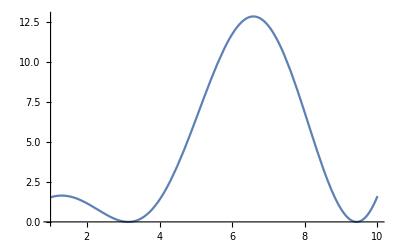

```mathematica
Plot[x*(1+Cos[x]),{x,1,10}]
```

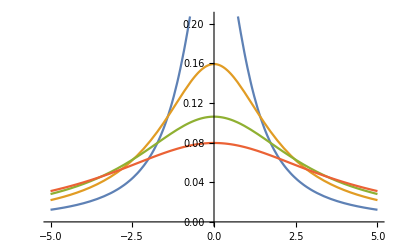

```mathematica
Plot[Table[PDF[CauchyDistribution[0,b],x],{b,1,4}]//Evaluate,{x,-5,5}]
```